# KS Initial conditions

## Metric

```mathematica
ClearAll[r,H,lx,ly,lz];
r[x_,y_,z_]:=√(1/2(x^2+y^2+z^2-a^2)+√(1/4(x^2+y^2+z^2-a^2)^2+a^2 z^2));
H[x_,y_,z_]:=(M*r[x,y,z]^3)/(r[x,y,z]^4+a^2*z^2);

lx[x_,y_,z_]:=(r[x,y,z]*x+a*y)/(r[x,y,z]^2+a^2)
ly[x_,y_,z_]:=(r[x,y,z]*y-a*x)/(r[x,y,z]^2+a^2)
lz[x_,y_,z_]:=z/r[x,y,z];

ClearAll[l];
l[x_,y_,z_]:={1,lx[x,y,z],ly[x,y,z],lz[x,y,z]};

ClearAll[η];
η=DiagonalMatrix[{-1,1,1,1}];

ClearAll[llgKS];
llgKS=η+Table[2*H[x,y,z]l[x,y,z]⟦i⟧l[x,y,z]⟦j⟧,{i,1,4},{j,1,4}];
```

## Initial data ellipse

```mathematica
ClearAll[elipseID];
elipseID[BHParams_,InitPos_,LocalEnergy_,ParticleMass_,param_]:=Module[
{llg,En,m,LEPUM,velNorm,AA,BB,CC,DD,FF,GG,Δ,J,II,α,β,X0,Y0,θ},

llg=llgKS//.{
M->BHParams⟦1⟧,
a->BHParams⟦2⟧,

x->InitPos⟦1⟧,
y->InitPos⟦2⟧,
z->0
};

En=LocalEnergy;
m=ParticleMass;

LEPUM=En/m;
velNorm=1-(1/LEPUM)^2;

AA=llg⟦2,2⟧;
BB=llg⟦2,3⟧;
CC=llg⟦3,3⟧;
DD=0;
FF=0;
GG=-velNorm;

Δ=Det[{{AA,BB,DD},{BB,CC,FF},{DD,FF,GG}}];
J=Det[{{AA,BB},{BB,CC}}];
II=AA+CC;

If[!(Δ≠0&&J>0&&Δ/II<0),
Print["Unphysical configuration"];
Abort[];
];

X0=(CC*DD-BB*FF)/(BB^2-AA*CC);
Y0=(AA*FF-BB*DD)/(BB^2-AA*CC);

α=√((2(AA*FF^2+CC*DD^2+GG*BB^2-2*BB*DD*FF-AA*CC*GG))/((BB^2-AA*CC)(√((AA-CC)^2+4*BB^2)-(AA+CC))));
β=√((2(AA*FF^2+CC*DD^2+GG*BB^2-2*BB*DD*FF-AA*CC*GG))/((BB^2-AA*CC)(-√((AA-CC)^2+4*BB^2)-(AA+CC))));

θ=Piecewise[
{
{0,BB==0&&AA<CC},
{π/2,BB==0&&AA>CC},
{ArcCot[(AA-CC)/(2BB)]/2,BB≠0&&AA<CC},
{π/2+ArcCot[(AA-CC)/(2BB)]/2,BB≠0&&AA>CC}
}
];

Return[{X0+α Cos[param] Cos[θ]-β Sin[param] Sin[θ],Y0+β Cos[θ] Sin[param]+α Cos[param] Sin[θ]}];
]
```

```mathematica
ClearAll[ellipsePlot];
ellipsePlot[curve_,pt_]:=ParametricPlot[
curve,
{p,0,2π},

PlotRange->{{-1,1},{-1,1}},
PlotStyle->Directive[Black,Thick],

Axes->False,
Frame->True,

FrameLabel->{"Vx","Vy"},

Epilog->{
PointSize[Large],
Red,
Point[curve//.p->0],
Point[curve//.p->π],

Blue,
Point[curve//.p->π/2],
Point[curve//.p->3π/2],

Black,
Arrow[{{0,0},pt}],
Point[pt]
}
];
```

## Single trajectory

Vx = 0.7291093057269979
Vy = 0.6106076717772263

-------------------------

Vx = 0.5230892749033197
Vy = -0.369035585151868

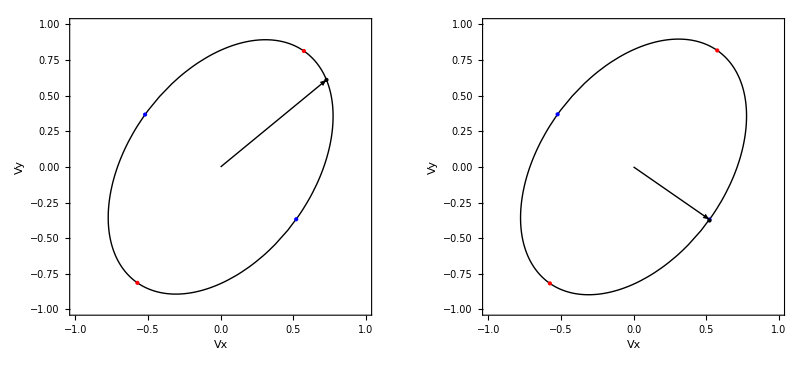

```mathematica
Block[
{M,a,x0,y0,En1,m1,En2,m2,X0,Y0,α,β,θ,curve1,curve2,pt1,pt2},
M=1;
a=98/100M;

x0=17/10;
y0=0;

En1=1;
m1=10^(-1);

En2=805/100*10^(-3);
m2=1*10^(-4);

curve1=elipseID[{M,a},{x0,y0},En1,m1,p];
curve2=elipseID[{M,a},{x0,y0},En2,m2,p];

pt1=curve1//.p->-25/200*π;
pt2=curve2//.p->-100/200*π;

Print["Vx = ",N[pt1⟦1⟧,16],"\nVy = ",N[pt1⟦2⟧,16]];
Print["-------------------------"];
Print["Vx = ",N[pt2⟦1⟧,16],"\nVy = ",N[pt2⟦2⟧,16]];

GraphicsRow[{ellipsePlot[curve1,pt1],ellipsePlot[curve2,pt2]}]
]
```